Jonas Neundorf, Jan Skottke

# Blatt 5, zweite Ausgabe

```mathematica
transportMatrix[Ψ_] := {{√(β2/β1)(Cos[Ψ] + αp*Sin[Ψ]), √(β1*β2)Sin[Ψ]}, {((α1 - α2)Cos[Ψ] -(1+α1*α2)Sin[Ψ])/(√(β1*β2)), √(β2/β1)(Cos[Ψ] - α2*(Sin[Ψ]))}}
```

```mathematica
bmat={{β0,-α0},{-α0,γ0}}
```

(β0 | -α0
-α0 | γ0)

Vergewissern wir uns nun, das nach einer Umrundung die Twissparameter die Gleichen sind wie Vorher:

Wir erfinden nun ein paar Parameter

```mathematica
params = {βp ->18.8, βk->10.6, αp->-1.0, αk->0.5, ϵ->3.0*10^-8, μ->23.27409747201 (* Phasenvorschub pro Umlauf*)}
```

{βp→18.8,βk→10.6,αp→-1.,αk→0.5,ϵ→3.×10^-8,μ→23.2741}

definieren uns Ersetzungsregeln für β1 und β2 für die jeweiligen Abschnitte

```mathematica
leg1 = {α1->αp, α2->αk, β1->βp, β2->βk}
```

{α1→αp,α2→αk,β1→βp,β2→βk}

```mathematica
leg2 = {α1->αk, α2->αp, β1->βk, β2->βp}
```

{α1→αk,α2→αp,β1→βk,β2→βp}

```mathematica
tmat1[Ψ_] := transportMatrix[Ψ] //.leg1;
tmat2[Ψ_]:= transportMatrix[Ψ] //.leg2
```

legen willkürlich fest, dass der Phasenvorschub vom Pickup zum Kicker 5/2 π beträgt, also etwa ein Drittel des Umfangs

```mathematica
twissPickup = {α0->αp, β0->βp, γ0->γp}
```

{α0→αp,β0→βp,γ0→γp}

und prüfen, ob die Transportmatrix eigenltich stabil ist, d.h. de Betrag ihrer Spur kleiner als 2 ist.

```mathematica
Abs[Tr[tmat2[μ - n*π/2].tmat1[n*π/2] //.twissPickup //.γp->(1+αp^2)/βp//.n->5//.params]]
```

0.141944

Sie ist stabil. Nach einem vollen Umlauf sollten die Twiss-Parameter sich nicht geändert haben

```mathematica
{tmat1[0] //.γp->(1+αp^2)/βp//.n->5//.params} =={tmat2[μ - n*π/2].tmat1[n*π/2] //.γp->(1+αp^2)/βp//.n->5//.params}
```

False

haben sie aber. Hmpf.

```mathematica
tmat1[0] //.γp->(1+αp^2)/βp//.n->5//.params
```

(0.750886 | 0
-0.106257 | 0.750886)

```mathematica
tmat2[μ - n*π/2].tmat1[n*π/2] //.γp->(1+αp^2)/βp//.n->5//.params
```

(1.1008 | -24.8682
0.115893 | -1.24275)

```mathematica
kicker[g_] := {{1, 0}, {0, -g}} (*sollte so funktionieren*)
```

```mathematica
kickedTransport[g_] := tmat2[μ - n*π/2].kicker[g]tmat1[n*π/2] //.γp->(1+αp^2)/βp//.n->5//. params
```

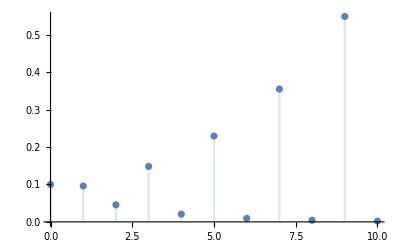

```mathematica
DiscretePlot[(MatrixPower[kickedTransport[-.005], n].{0.1, -0.1})[[1]], {n, 0,10}]  (*MatrixPower für Potenzen von Matrizen nehmen, weil der normale Potenzoperator nur die Elemente potenziert*)
```

Das ist merkwürdig, dass bei gerader Umlaufzahl die Ablage steigt, bei ungerader aber sinkt. Könnte mit der fehlerhaften Transportmatrix zu tun haben

```mathematica
m = tmat2[μ - n*π/2].kicker[.1]tmat1[n*π/2]//.γp->(1+αp^2)/βp//.n->5//. params
```

(1.24275 | -5.65734
0.00396485 | -0.0337484)

```mathematica
m = {{a, b}, {c, d}}
```

(a | b
c | d)

```mathematica
m.m
```

(a^2+b c | a b+d b
a c+d c | d^2+b c)

```mathematica
MatrixPower[m, 0]
```

(1 | 0
0 | 1)

```mathematica
data = RandomVariate[d= MultinormalDistribution[{.1, -.1}, {{0.02, 0.01}, {0.01, 0.02}}], 10^1] ;
```

```mathematica
Manipulate[Histogram3D[MatrixPower[kickedTransport[-.005], n].data], {n, 0, 10}]
```

Dot::dotsh: Tensors (1. | 0.
0. | 1.) and (-0.110668 | -0.42767
0.226778 | -0.182024
0.337209 | 0.00862339
0.157599 | -0.0927879
0.098492 | 0.0304372
-0.162098 | -0.2883
0.0542651 | -0.289827
0.128008 | -0.214002
0.0368233 | -0.00602585
0.26885 | 0.186287) have incompatible shapes.

Histogram3D::ldata: (1. | 0.
0. | 1.).(-0.110668 | -0.42767
0.226778 | -0.182024
0.337209 | 0.00862339
0.157599 | -0.0927879
0.098492 | 0.0304372
-0.162098 | -0.2883
0.0542651 | -0.289827
0.128008 | -0.214002
0.0368233 | -0.00602585
0.26885 | 0.186287) is not a valid dataset or list of datasets.